10.6

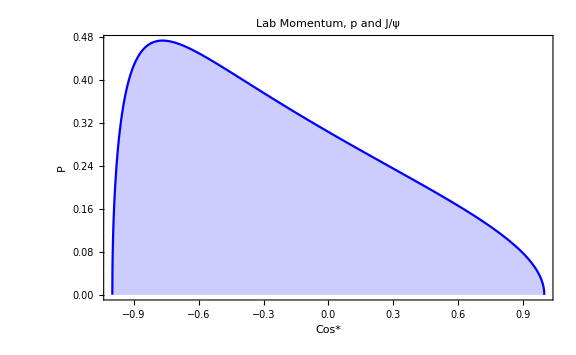

```mathematica
color1=Blue;
color2=Red;
ebeam=10.6;
mp           = 0.93827231 ;
mjpsi       = 3.096917 ;
ms2[eg_]:=2*eg*mp+mp^2;
ms[eg_]:=Sqrt[ms2[eg]];

ejpsis[eg_]:=(ms2[eg]+mjpsi^2-mp^2)/(2 ms[eg]);
pjpsis[eg_]:=Sqrt[ejpsis[eg]^2-mjpsi^2];
eps[eg_]:=(ms2[eg]-mjpsi^2+mp^2)/(2 ms[eg]);
pps[eg_]:=pjpsis[eg];

gamma[eg_]:=(eg+mp)/ms[eg];
vel[eg_]:=eg/(eg+mp);

ppz[eg_,cos_]:=gamma[eg](pps[eg]*cos+vel[eg]eps[eg]);
ppx[eg_,cos_]:=pps[eg] Sqrt[1-cos^2];
pjpsiz[eg_,cos_]:=gamma[eg](-pjpsis[eg]*cos+vel[eg]ejpsis[eg]);

cs=1.;
eb=10.6
Plot[{ppx[eb,cs]/ppz[eb,cs]},                     {cs,-1,1},
PlotLabel->"Lab Momentum, p and  J/ψ",
Frame ->True, FrameLabel->{"Cos*","P"},
Filling->Axis,
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
```